Percolation 

Introduction 
Percolation theory is a branch of statistical physics and mathematics studying the behavior of connected clusters in a random graph or lattice. It models fluid flow through porous materials, disease spread, or network reliability. The central parameter is the occupation probability, p. Increasing p leads to a phase transition (critical phenomenon) where small, disconnected clusters merge to form a “spanning cluster” connecting opposite sides of the system.

Creating a Dynamic Grid
The variable n defines the system size. Manipulate creates an interactive interface to dynamically adjust the grid dimension L (variable n) from 10 to 50. ArrayPlot visualizes an n × n matrix of zeros, representing an empty lattice.

```mathematica
n=10;
Manipulate[ArrayPlot[Table[0,{n},{n}],Mesh->True,Frame->True,FrameTicks->None,PlotLabel->Style["Grid size: "<>ToString[n]<>"x"<>ToString[n],14]],{{n,10,"Grid dimension L"},5,50,1,Appearance->"Labeled"}]
```

```mathematica
(_□)_((□_□)_□)
```

Populating the Grid
In “site percolation,” each site on the lattice is either occupied (conductive/open) or empty (blocked/closed) based on a probability p. RandomChoice populates the n × n grid, assigning values based on weights {p, 1-p}.

• Probability p: Determines the density of occupied sites.
• Manipulate Interface: A slider controls p (ranging from 0 to 1) alongside a “Refresh” button.
• Visualization: ArrayPlot displays the resulting random configuration. This static noise visualization verifies site distribution behavior before clustering algorithms are applied.

```mathematica
Manipulate[refresh;ArrayPlot[RandomChoice[{p,1-p}->{0,2},{n,n}],Mesh->True,Frame->True,FrameTicks->None,PlotLabel->Style["Grid size: "<>ToString[n]<>"x"<>ToString[n]<>" | p = "<>ToString[p],14]],{{n,10,"Grid dimension L"},5,100,1,Appearance->"Labeled"},{{p,0.5,"Probability p"},0.1,0.9,0.05,Appearance->"Labeled"},{{refresh,0},None},Button["Refresh",refresh++]]
```

Single Cluster Evolution

The Propagation Algorithm
Starting from a seed site, nearest neighbors (Up, Down, Left, Right) are iteratively checked. If a neighbor is occupied, it joins the active cluster.

• PercolationStep: Performs one iteration of growth. RotateLeft and RotateRight efficiently shift the matrix to compare neighbors, identifying and activating neighbors of “active” cells (state 1).
• PercolationEvolution: Sets up the simulation. A single active site is seeded in the center. NestWhileList repeatedly applies the step function until the grid stops changing, indicating the cluster has reached maximum extent.
• Visualization: An animation shows the time-evolution of a single cluster growing outwards.

```mathematica
(*single step that fill the nearest neighbours*)
PercolationStep[n_,p_,prevState_]:=
Module[{newState},newState=prevState;

newState=prevState;

tmp=prevState+RotateLeft[prevState,{1,0}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateRight[prevState,{1,0}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateLeft[prevState,{0,1}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateRight[prevState,{0,1}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
newState]

(*function that create the list of configurations for different time step*)
PercolationEvolution[n_,p_]:=Module[{initialState,center,evolution},
initialState=RandomChoice[{p,1-p}->{0,-10},{n,n}];
initialState[[Ceiling[n/2],Ceiling[n/2]]]=1;
initialState=ArrayPad[initialState,1,-10];
evolution=NestWhileList[PercolationStep[n,p,#]&,initialState,#1!=#2&,2];
evolution]

(*ArrayPlot to isualize with manipulate the different cofnigurations*)
VisualizePercolation[state_,step_]:=ArrayPlot[state,ColorRules->{0->White,1->Blue,-10->Black,-5->Red},Mesh->True,Frame->True,FrameTicks->None,PlotLabel->Style["Step: "<>ToString[step]<>" | Occupied sites: "<>ToString[Count[state,1,2]],14]]

(*Manipulate that allows visualizing different configuration base on the time step*)
Manipulate[refresh;
Module[{evolution,frames},evolution=PercolationEvolution[n,p];
frames=Table[VisualizePercolation[evolution[[t]],t-1],{t,1,Length[evolution]}];
ListAnimate[frames,AnimationRunning->False,AnimationRepetitions->1]],{{n,30,"Grid dimension L"},8,50,1,Appearance->"Labeled"},{{p,0.45,"Probability p"},0.35,0.85,0.01,Appearance->"Labeled"},{{refresh,0},None},Button["New Simulation",(t=1;refresh++)],
SynchronousUpdating->False]
```

Multi-Cluster Analysis and Size Distribution

Cluster Counting and Statistics
Physical systems analysis focuses on the distribution of all cluster sizes, not just a single central one. Determining the percolation threshold (pc) involves measuring the count and size of clusters.

Iterative Cluster Identification
The logic is refined to analyze the entire grid:
1. Iterative Search: A cluster grows from a random seed.
2. Archiving: When growth stops (If[newState == prevState]), the size is recorded in clusterSize.
3. State Change: The finished cluster is marked with a new value (e.g., -5, rendered in Red) to prevent recounting.
4. Re-seeding: A new, unvisited occupied site (Position[..., 0]) is found, and the process repeats.
This loop continues until all occupied sites are assigned to a cluster, allowing for the construction of a histogram of cluster sizes.

```mathematica
clusterSize={};   (*list to plot the histogram of the size of the clusters*)

(*single step that fill the nearest neighbours*)
PercolationStep2[n_,p_,prevState_]:=Module[{newState,tmp},newState=prevState;
tmp=prevState+RotateLeft[prevState,{1,0}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateRight[prevState,{1,0}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateLeft[prevState,{0,1}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
tmp=prevState+RotateRight[prevState,{0,1}];
newState=ReplacePart[newState,Thread[Position[tmp,1]->1]];
If[newState==prevState,If[Count[Flatten[newState],1]!=0,clusterSize=Append[clusterSize,Count[Flatten[newState],1]]];
newState=ReplacePart[newState,Thread[Position[newState,1]->-5]];
If[MemberQ[Flatten[newState],0],newState=ReplacePart[newState,RandomChoice[Position[newState,0]]->1]]];
newState];

(*function that create the list of configurations for different time step*)
PercolationEvolution2[n_,p_]:=PercolationEvolution2[n,p]=Module[{initialState,evolution},initialState=RandomChoice[{p,1-p}->{0,-10},{n,n}];
initialState=ArrayPad[initialState,1,-10];
clusterSize={};
If[MemberQ[Flatten[initialState],0],initialState=ReplacePart[initialState,RandomChoice[Position[initialState,0]]->1]];
evolution=NestWhileList[PercolationStep2[n,p,#]&,initialState,#1!=#2&,2];
evolution];

(*ArrayPlot to isualize with manipulate the different cofnigurations*)
VisualizePercolation2[state_,step_]:=ArrayPlot[state,ColorRules->{0->White,1->Blue,-10->Black,-5->Red},Mesh->True,Frame->True,FrameTicks->None,PlotLabel->Style["Step: "<>ToString[step]<>" | Occupied sites: "<>ToString[Count[state,1,2]],14]];

(*Manipulate that allows visualizing different configuration base on the time step*)
Manipulate[refresh;
Module[{evolution,frames},evolution=PercolationEvolution2[n,p];
frames=Table[VisualizePercolation2[evolution[[t]],t-1],{t,1,Length[evolution]}];
ListAnimate[frames,AnimationRunning->False,AnimationRepetitions->1]],{{n,45,"Grid dimension L"},8,50,1,Appearance->"Labeled"},{{p,0.60,"Probability p"},0.35,0.85,0.01,Appearance->"Labeled"},{{refresh,0},None},Button["New Simulation",(t=1;refresh++)],
SynchronousUpdating->False]
```

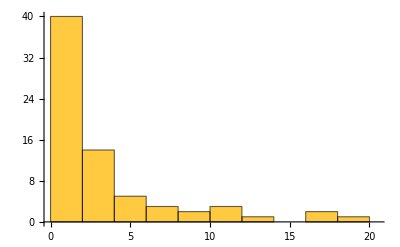

```mathematica
Histogram[clusterSize]
```